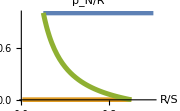
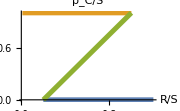

```mathematica
SetDirectory[NotebookDirectory[]];
R0=1;
S0=2;
β=.2;
λ=100;
tmax=4.2;

(*state variables*)
vars={
R,(* root biomass  *)
S ,(* shoot biomass  *)
XN,(* nitrogen shared: buffer *)
XC (* carbon shared: buffer *)
};

(* Synthesizing Unit  *)

F[x_,y_]:=Min[x,y];

(*growth rate of root and shoot*)

UN=R;
UC=S;

jRG=F[XC,UN];
jSG=F[UC,XN/β];

(*N and C shared (unbuffered)*)

jN=UN-jRG;
jC=UC-jSG;

(*ODEs: root and shoot biomass, shared N and C (buffered)*)
eqs=(#[[1]]==(#[[2]]/.(#->#[t]&/@vars)))&/@{
R'[t]==jRG,
S'[t]==jSG,
XN'[t]==λ (jN-XN),
XC'[t]==λ (jC-XC)
};



(*plots*)
fluxsol=Quiet@NSolve[{XN==jN,XC==jC},{XC,XN}];
style={LabelStyle->10,ImageSize->Small,PlotStyle->({#,Thickness[.02]}&/@(ColorData[97]/@{2,1,3}))};
Row[{(Export["root-shoot-bifurcations-rhoN.pdf",#];#)&@Plot[Evaluate[(XN/R) /.fluxsol/.S->1],{R,.01,1.2},AxesLabel->{"StyleBox[\"R\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"S\",FontSlant->\"Italic\"]"},PlotRange->Full,PlotLabel->"ρ_NStyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"R\",FontSlant->\"Italic\"]",Evaluate@style],
(Export["root-shoot-bifurcations-rhoC.pdf",#];#)&@Plot[Evaluate[(XC/S) /.fluxsol/.S->1],{R,.01,1.2},AxesLabel->{"StyleBox[\"R\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"S\",FontSlant->\"Italic\"]"},PlotRange->Full,PlotLabel->"SubscriptBox[\"ρ\", StyleBox[\"C\",FontSlant->\"Italic\"]]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"S\",FontSlant->\"Italic\"]",Evaluate@style]}]
```

```mathematica
simulate[inis_]:=NDSolve[
{eqs,inis},
vars,
{t,0,tmax}
];
```

```mathematica
xmax=25;
style2={LabelStyle->12,ImageSize->Small,PlotStyle->Thickness[.025]};
(*solve the ODEs*)
sol1=
simulate[{
R[0]==R0,
S[0]==S0,
XN[0]==R0,
XC[0]==0
}];
sol2=simulate[{
R[0]==R0,
S[0]==S0,
XN[0]==0,
XC[0]==S0
}];
```

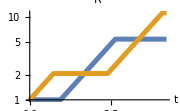
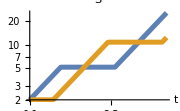
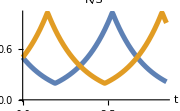
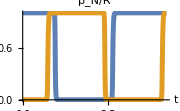
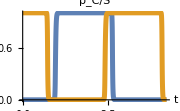

```mathematica
fontfamily="Times";
plotcols=ColorData[97]/@Range[2];
timeplotstyle={AxesOrigin->{0,0},ImageSize->Small,PlotStyle->({#,Thickness[.02]}&/@plotcols),AxesLabel->{"t"},LabelStyle->{FontFamily->fontfamily,FontSize->16}(*,Ticks->{Charting`ScaledTicks[{Identity,Identity}][##,{4,4}]&,Automatic(*Charting`ScaledTicks[{Identity,Identity}][##,{3,3}]&*)}*)};
doplots[sols_(*,maxSoverH_,minSandH_,maxSandH_*)]:=Style[Column[
{Row@Join[
(*plot S/H ratio*)

(*plot all state variables*)

Table[LogPlot[Evaluate[x[t]/.sols],{t,0,tmax},PlotLabel->(x/.{R->"R",S->"S"}),Evaluate@timeplotstyle,PlotRange->Automatic(*{minSandH,maxSandH}*)],{x,{R,S}}],
{Plot[Evaluate[{R[t]/S[t]}/.sols],{t,0,tmax},PlotLabel->"R/S",Evaluate@timeplotstyle,PlotRange->Automatic(*{0,maxSoverH}*)]}
],
Row@Table[Plot[Evaluate@Flatten@{Max[0,x]/.sols},{t,0,tmax},PlotLabel->Style[x/.{XN[t]/R[t]->"ρ_N/R",XC[t]/S[t]->"ρ_C/S"},Italic],Evaluate@timeplotstyle,PlotRange->Automatic(*{x/.{jCP->{0,1.05jCPm},jSG->{0,jSGm}}/.parvals}*)],{x,{XN[t]/R[t],XC[t]/S[t]}}]}
,Alignment->Center],LineBreakWithin->False];
(Export["root-shoot-simu.pdf",#];#)&@doplots[{sol1,sol2}]
```

```mathematica
(Export[NotebookDirectory[]<>"root-shoot-simulation-legend.pdf",#];#)&@Column[{
Style["Initializiation",FontFamily->fontfamily],
Grid[Table[Flatten@{Plot[1/2,{x,0,1},PlotRange->{0,1},PlotStyle->{Thickness[.15],plotcols[[i]]},Axes->None,ImageSize->20],Spacer[1],Style[#[[i]],FontFamily->fontfamily]&/@{{"ρ_N(0) = 1    ","ρ_N(0) = 0    "},{"ρ_C(0) = 0    ","ρ_C(0) = 1    "}}},{i,2}],Alignment->Left]},Alignment->Center]
```

Initializiation
-Graphics- |  | ρ_N(0) = 1     | ρ_C(0) = 0    
-Graphics- |  | ρ_N(0) = 0     | ρ_C(0) = 1